```mathematica
(*css zebrafinch model*)
(*recursions*)
ns := Na ba pa + Nn bn pn;
nh:= Na ba (1-pa) + Nn bn (1-pn);
NNa :=ns vs((1-lsO) vI z +lsO qO ) + nh vh((1-lhO) vI z +lhO qO );
NNn :=ns vs((1-lsO) vI (1-z)+lsO(1- qO) ) + nh vh((1-lhO) vI (1-z)+lhO(1- qO) );
qO := (1-u)(Na/(Na +Nn));
```

```mathematica
AA:=({{0, 0, ba pa, bn pn}, {0, 0, ba(1-pa), bn(1-pn)}, {vs((1-lsO) vI z +lsO qO ), vh((1-lhO) vI z +lhO qO ), 0, 0}, {vs((1-lsO) vI (1-z)+lsO(1- qO) ), vh((1-lhO) vI (1-z)+lhO(1- qO) ), 0, 0}})
```

```mathematica
NN = FullSimplify[NNn + NNa];
```

```mathematica
FFa=FullSimplify[NNa/NN/.{Na->Fa N0,Nn->(1-Fa)N0}];
```

```mathematica
FFn=FullSimplify[NNn/NN/.{Na->Fa N0,Nn->(1-Fa)N0}];
```

```mathematica
Simplify[FFn+FFa]
```

1

```mathematica
Fasols=Solve[FFa==Fa,Fa]
```

{{Fa→(bn lhO u vh-bn lhO pn u vh+bn vh vI-bn lhO vh vI-bn pn vh vI+bn lhO pn vh vI+bn lsO pn u vs+bn pn vI vs-bn lsO pn vI vs-ba vh vI z+bn vh vI z+ba lhO vh vI z-bn lhO vh vI z+ba pa vh vI z-ba lhO pa vh vI z-bn pn vh vI z+bn lhO pn vh vI z-ba pa vI vs z+ba lsO pa vI vs z+bn pn vI vs z-bn lsO pn vI vs z-√(-4 (-ba lhO u vh+bn lhO u vh+ba lhO pa u vh-bn lhO pn u vh-ba vh vI+bn vh vI+ba lhO vh vI-bn lhO vh vI+ba pa vh vI-ba lhO pa vh vI-bn pn vh vI+bn lhO pn vh vI-ba lsO pa u vs+bn lsO pn u vs-ba pa vI vs+ba lsO pa vI vs+bn pn vI vs-bn lsO pn vI vs) (bn vh vI z-bn lhO vh vI z-bn pn vh vI z+bn lhO pn vh vI z+bn pn vI vs z-bn lsO pn vI vs z)+(-bn lhO u vh+bn lhO pn u vh-bn vh vI+bn lhO vh vI+bn pn vh vI-bn lhO pn vh vI-bn lsO pn u vs-bn pn vI vs+bn lsO pn vI vs+ba vh vI z-bn vh vI z-ba lhO vh vI z+bn lhO vh vI z-ba pa vh vI z+ba lhO pa vh vI z+bn pn vh vI z-bn lhO pn vh vI z+ba pa vI vs z-ba lsO pa vI vs z-bn pn vI vs z+bn lsO pn vI vs z)^2))/(2 (-ba lhO u vh+bn lhO u vh+ba lhO pa u vh-bn lhO pn u vh-ba vh vI+bn vh vI+ba lhO vh vI-bn lhO vh vI+ba pa vh vI-ba lhO pa vh vI-bn pn vh vI+bn lhO pn vh vI-ba lsO pa u vs+bn lsO pn u vs-ba pa vI vs+ba lsO pa vI vs+bn pn vI vs-bn lsO pn vI vs))},{Fa→(bn lhO u vh-bn lhO pn u vh+bn vh vI-bn lhO vh vI-bn pn vh vI+bn lhO pn vh vI+bn lsO pn u vs+bn pn vI vs-bn lsO pn vI vs-ba vh vI z+bn vh vI z+ba lhO vh vI z-bn lhO vh vI z+ba pa vh vI z-ba lhO pa vh vI z-bn pn vh vI z+bn lhO pn vh vI z-ba pa vI vs z+ba lsO pa vI vs z+bn pn vI vs z-bn lsO pn vI vs z+√(-4 (-ba lhO u vh+bn lhO u vh+ba lhO pa u vh-bn lhO pn u vh-ba vh vI+bn vh vI+ba lhO vh vI-bn lhO vh vI+ba pa vh vI-ba lhO pa vh vI-bn pn vh vI+bn lhO pn vh vI-ba lsO pa u vs+bn lsO pn u vs-ba pa vI vs+ba lsO pa vI vs+bn pn vI vs-bn lsO pn vI vs) (bn vh vI z-bn lhO vh vI z-bn pn vh vI z+bn lhO pn vh vI z+bn pn vI vs z-bn lsO pn vI vs z)+(-bn lhO u vh+bn lhO pn u vh-bn vh vI+bn lhO vh vI+bn pn vh vI-bn lhO pn vh vI-bn lsO pn u vs-bn pn vI vs+bn lsO pn vI vs+ba vh vI z-bn vh vI z-ba lhO vh vI z+bn lhO vh vI z-ba pa vh vI z+ba lhO pa vh vI z+bn pn vh vI z-bn lhO pn vh vI z+ba pa vI vs z-ba lsO pa vI vs z-bn pn vI vs z+bn lsO pn vI vs z)^2))/(2 (-ba lhO u vh+bn lhO u vh+ba lhO pa u vh-bn lhO pn u vh-ba vh vI+bn vh vI+ba lhO vh vI-bn lhO vh vI+ba pa vh vI-ba lhO pa vh vI-bn pn vh vI+bn lhO pn vh vI-ba lsO pa u vs+bn lsO pn u vs-ba pa vI vs+ba lsO pa vI vs+bn pn vI vs-bn lsO pn vI vs))}}

```mathematica
subtest = {ba->3,bn->1,z->0.6,pa->0.1,pn->0.9,vs->0.8,vh->0.95,vI->0.7  ,lsO-> 0.2 ,lsV-> 0 ,lsI-> 0.8,lhO-> 0.8,lhI-> 0.2 ,u-> 0.1 };
```

```mathematica
Fasols[[1,1,2]]/.subtest (*check it is stable qhat with values, select positive q-hat*)
 Simplify[Fasols[[1,1,2]]/.{lhO->LHO,lhI -> LHI, lsO -> LSO, lsI-> LSI}](*copy and paste solution below*)
 Fasols/.subtest
```

0.480835

(bn LHO u vh-bn LHO pn u vh+bn vh vI-bn LHO vh vI-bn pn vh vI+bn LHO pn vh vI+bn LSO pn u vs+bn pn vI vs-bn LSO pn vI vs-ba vh vI z+bn vh vI z+ba LHO vh vI z-bn LHO vh vI z+ba pa vh vI z-ba LHO pa vh vI z-bn pn vh vI z+bn LHO pn vh vI z-ba pa vI vs z+ba LSO pa vI vs z+bn pn vI vs z-bn LSO pn vI vs z-√(-4 bn vI ((-1+LHO) (-1+pn) vh-(-1+LSO) pn vs) (ba (LHO (-1+pa) vh (u-vI)+(-1+pa) vh vI-pa (LSO u+vI-LSO vI) vs)+bn (-LHO (-1+pn) vh (u-vI)+vh (vI-pn vI)+pn (LSO u+vI-LSO vI) vs)) z+(ba vI ((-1+LHO) (-1+pa) vh-(-1+LSO) pa vs) z+bn ((-1+pn) vh vI (1+z)+LHO (-1+pn) vh (u-vI (1+z))-pn vs (vI (1+z)+LSO (u-vI (1+z)))))^2))/(2 (ba (LHO (-1+pa) vh (u-vI)+(-1+pa) vh vI-pa (LSO u+vI-LSO vI) vs)+bn (-LHO (-1+pn) vh (u-vI)+vh (vI-pn vI)+pn (LSO u+vI-LSO vI) vs)))

{{Fa→0.480835},{Fa→-1.96121}}

```mathematica
(*make QHAT a function of css states*)
```

```mathematica
QHAT[LHO_,LSO_] := (bn LHO u vh-bn LHO pn u vh+bn vh vI-bn LHO vh vI-bn pn vh vI+bn LHO pn vh vI+bn LSO pn u vs+bn pn vI vs-bn LSO pn vI vs-ba vh vI z+bn vh vI z+ba LHO vh vI z-bn LHO vh vI z+ba pa vh vI z-ba LHO pa vh vI z-bn pn vh vI z+bn LHO pn vh vI z-ba pa vI vs z+ba LSO pa vI vs z+bn pn vI vs z-bn LSO pn vI vs z-√(-4 bn vI ((-1+LHO) (-1+pn) vh-(-1+LSO) pn vs) (ba (LHO (-1+pa) vh (u-vI)+(-1+pa) vh vI-pa (LSO u+vI-LSO vI) vs)+bn (-LHO (-1+pn) vh (u-vI)+vh (vI-pn vI)+pn (LSO u+vI-LSO vI) vs)) z+(ba vI ((-1+LHO) (-1+pa) vh-(-1+LSO) pa vs) z+bn ((-1+pn) vh vI (1+z)+LHO (-1+pn) vh (u-vI (1+z))-pn vs (vI (1+z)+LSO (u-vI (1+z)))))^2))/(2 (ba (LHO (-1+pa) vh (u-vI)+(-1+pa) vh vI-pa (LSO u+vI-LSO vI) vs)+bn (-LHO (-1+pn) vh (u-vI)+vh (vI-pn vI)+pn (LSO u+vI-LSO vI) vs)));
```

```mathematica
AA2=AA/.{Na->Qh,Nn->(1-Qh)};
```

```mathematica
LL=Eigenvalues[AA2];
```

```mathematica
LV=Eigenvectors[AA2];
```

```mathematica
LL/.subtest /. Qh -> 0.5 (*sub in rando qhat value to identify positive eigen values*)
```

{0.-0.267951 ⅈ,0.+0.267951 ⅈ,-1.26511,1.26511}

```mathematica
(*eigenvectors give one ratios of stage/stress classes*) 
LV/.subtest /. Qh -> 0.5
```

{{0.+3.06129 ⅈ,0.-2.3046 ⅈ,-0.265748,1},{0.-3.06129 ⅈ,0.+2.3046 ⅈ,-0.265748,1},{-0.941609,-2.15091,0.970791,1},{0.941609,2.15091,0.970791,1}}

```mathematica
Simplify[LL[[4]]]
```

1/(√2)(√(bn lhO vh-bn lhO pn vh+ba lhO Qh vh-bn lhO Qh vh-ba lhO pa Qh vh+bn lhO pn Qh vh-ba lhO Qh u vh+bn lhO Qh u vh+ba lhO pa Qh u vh-bn lhO pn Qh u vh+bn vh vI-bn lhO vh vI-bn pn vh vI+bn lhO pn vh vI+bn lsO pn vs+ba lsO pa Qh vs-bn lsO pn Qh vs-ba lsO pa Qh u vs+bn lsO pn Qh u vs+bn pn vI vs-bn lsO pn vI vs+ba vh vI z-bn vh vI z-ba lhO vh vI z+bn lhO vh vI z-ba pa vh vI z+ba lhO pa vh vI z+bn pn vh vI z-bn lhO pn vh vI z+ba pa vI vs z-ba lsO pa vI vs z-bn pn vI vs z+bn lsO pn vI vs z+√(-4 ba bn (lhO-lsO) (pa-pn) vh vI vs (Qh (-1+u)+z)+(bn (lhO (-1+pn) vh (1+Qh (-1+u)+vI (-1+z))+vh vI (-1+pn+z-pn z)-pn vs (lsO+lsO Qh (-1+u)+vI+lsO vI (-1+z)-vI z))+ba (vI ((-1+pa) vh-pa vs) z-lhO (-1+pa) vh (Qh (-1+u)+vI z)+lsO pa vs (Qh (-1+u)+vI z)))^2)))

```mathematica
(*isolate dominant eigenvalue*)
Lambda[ lsO_, lhO_,LHO_,LSO_]:=1/(√2)(√(bn lhO vh-bn lhO pn vh+ba lhO  QHAT[LHO,LSO] vh-bn lhO  QHAT[LHO,LSO] vh-ba lhO pa  QHAT[LHO,LSO] vh+bn lhO pn  QHAT[LHO,LSO] vh-ba lhO  QHAT[LHO,LSO] u vh+bn lhO  QHAT[LHO,LSO] u vh+ba lhO pa  QHAT[LHO,LSO] u vh-bn lhO pn  QHAT[LHO,LSO] u vh+bn vh vI-bn lhO vh vI-bn pn vh vI+bn lhO pn vh vI+bn lsO pn vs+ba lsO pa  QHAT[LHO,LSO] vs-bn lsO pn  QHAT[LHO,LSO] vs-ba lsO pa  QHAT[LHO,LSO] u vs+bn lsO pn  QHAT[LHO,LSO] u vs+bn pn vI vs-bn lsO pn vI vs+ba vh vI z-bn vh vI z-ba lhO vh vI z+bn lhO vh vI z-ba pa vh vI z+ba lhO pa vh vI z+bn pn vh vI z-bn lhO pn vh vI z+ba pa vI vs z-ba lsO pa vI vs z-bn pn vI vs z+bn lsO pn vI vs z+√(-4 ba bn (lhO-lsO) (pa-pn) vh vI vs ( QHAT[LHO,LSO] (-1+u)+z)+(bn (lhO (-1+pn) vh (1+ QHAT[LHO,LSO] (-1+u)+vI (-1+z))+vh vI (-1+pn+z-pn z)-pn vs (lsO+lsO  QHAT[LHO,LSO] (-1+u)+vI+lsO vI (-1+z)-vI z))+ba (vI ((-1+pa) vh-pa vs) z-lhO (-1+pa) vh ( QHAT[LHO,LSO] (-1+u)+vI z)+lsO pa vs ( QHAT[LHO,LSO] (-1+u)+vI z)))^2)))
```

```mathematica
(*use Lambda1 for general soln with pa and pn as parameters*)
DlsO=D[Lambda[lsO, lhO,LHO,LSO],lsO]/. {LHO -> lhO,LSO-> lsO};
```

```mathematica
DlhO=D[Lambda[lsO, lhO,LHO,LSO],lhO]/. {LHO -> lhO,LSO-> lsO};
```

```mathematica
(*try and graph*)

lsOstart=0.01;
lhOstart=0.01;
imax=1500;
lsItab=Table[0,{i,imax}];
lhItab=Table[0,{i,imax}];
lsOtab=Table[0,{i,imax}];
lhOtab=Table[0,{i,imax}];
DlsOtab=Table[0,{i,imax}];
DlhOtab=Table[0,{i,imax}];
delta=0.04;
sub2={ba->2,bn->1,z->0.8,vs->0.4,vh->0.9,vI->0.8  ,u->0.05, pa-> 0.1, pn-> 0.9};
lsOtab[[1]]=lsOstart;
lhOtab[[1]]=lhOstart;

DlsOtab[[1]]=DlsO/.sub2/.{lsO->lsOstart,lhO->lhOstart};
DlhOtab[[1]]=DlhO/.sub2/.{lsO->lsOstart,lhO->lhOstart};
```

```mathematica
For[i=2,i<imax,i++,{

lsOtab[[i]]=lsOtab[[i-1]]  + delta DlsO/.sub2/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lsOtab[[i]]=If[lsOtab[[i]]>1,1,lsOtab[[i]]];
lsOtab[[i]]=If[lsOtab[[i]]<0,0,lsOtab[[i]]];

lhOtab[[i]]=lhOtab[[i-1]]  + delta DlhO/.sub2/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lhOtab[[i]]=If[lhOtab[[i]]>1,1,lhOtab[[i]]];
lhOtab[[i]]=If[lhOtab[[i]]<0,0,lhOtab[[i]]];

DlsOtab[[i]]=DlsO/.sub2/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
DlhOtab[[i]]=DlhO/.sub2/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
}];
```

```mathematica
lsItab = 1-lsOtab;
lhItab = 1-lhOtab;
```

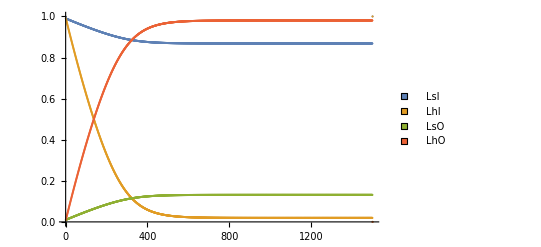

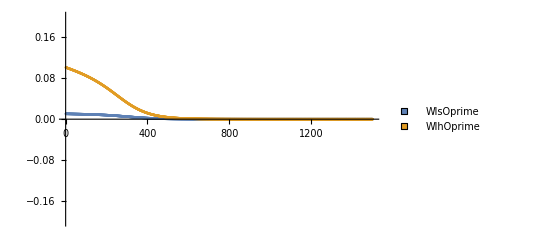

```mathematica
ListPlot[{lsItab,lhItab,lsOtab,lhOtab},PlotRange->{All,{0,1}},PlotLegends->PointLegend[{LsI,LhI,LsO,LhO},LegendMarkers->Graphics[Rectangle[]]]] 
ListPlot[{DlsOtab,DlhOtab},PlotRange->{All,{-0.2,0.2}},PlotLegends->PointLegend[{WlsOprime,WlhOprime},LegendMarkers->Graphics[Rectangle[]]]]
```